S. Patomäki 2016, 2017
sofia.patomaki@helsinki.fi

```mathematica
If[FreeQ[$Path,"/pathToQuantumMechanics.m/"],
AppendTo[$Path,"/pathToQuantumMechanics.m/"];
];
Needs["QuantumMechanics`"];
```

We numerically diagonalize the CPB Hamiltonian as a function of the offset charge and the phase.

Maximal offset charge dependence of the transition energy: 0.

Thus, we ignore ng-dependence.

Transition energy as a function of phi:

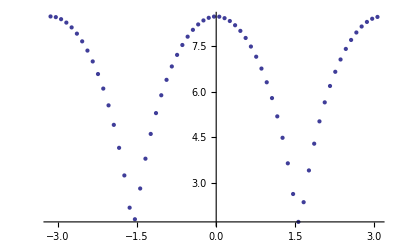

```mathematica
Clear[NQuantaCPB,EC,EJmax,NM,CosPhiM,dng,dphi,ng1,ng2,phi1,phi2,ngList,phiList,Energyeg,tol];
(*NquantaCPB: Maximum number of excitations in Cooper Pair Box (CPB).
Formally, it should be infinity, but a small number will do if the system is not 
far too excited. Note that there are both negative and positive eigenvalues,
as explained in the Appendix B of the thesis.*) 
NQuantaCPB=15; (*Because of the negative eigenvalues, odd number is more natural; no relevant change for NQuantaCPB>=17*)

(*Other CPB parameters (specific to a sample) in units of GHz:*)
EC=0.423;
EJmax=23.5;

(*Number operator*)
NM=Sum[(n-Floor[NQuantaCPB/2])×KetBraM[NQuantaCPB,n,n],{n,1,NQuantaCPB}]; 
(*CosPhi-operator in the number basis*)
CosPhiM=Sum[Sum[If[Abs[i-j]==1,KetBraM[NQuantaCPB,i,j],0],{i,1,NQuantaCPB}],{j,1,NQuantaCPB}]/2;

(*Loop over offset charge in steps of dng; phi in steps of dphi*)
dng=0.5;
ng1=-0.5;
ng2=0.5;
dphi=0.1;
phi1=-π;
phi2=π;
ngList=Table[ng,{ng,ng1,ng2,dng}];
phiList=Table[phi,{phi,phi1,phi2,dphi}];
Energyeg=Table[0,{ng,ng1,ng2,dng},{phi,phi1,phi2,dphi}];(*Transition energy*)
Do[
	Do[Clear[Ng,EJ,HamiltonianCPB,EigVals,EigVecs,gIndex,eIndex];
		(*Offset charge matrix*)
		Ng=ngList[[i]]×IdM[NQuantaCPB];
		
		(*Cooper Pair Box Hamiltonian (definitions found in Appendix B)*)
		EJ=EJmax×Cos[phiList[[j]]];(*Externally-tuned Josephson energy (Eq. 2.35)*)
		HamiltonianCPB=4×EC×MatrixPower[NM-IdM[NQuantaCPB],2]-EJ×CosPhiM;
	
		{EigVals,EigVecs}=Eigensystem[HamiltonianCPB,Cubics->True];
	
		(*Find the smallest eigenvalues (corresponding to g and e states)*)
		gIndex=Position[EigVals,Min[EigVals]][[1]][[1]];
		eIndex=Position[EigVals,Min[Delete[EigVals,gIndex]]][[1]][[1]];

		(*Fill in the transition energy*)
		Energyeg[[i,j]]=EigVals[[eIndex]]-EigVals[[gIndex]];
	,{i,1,Length[ngList]}];
,{j,1,Length[phiList]}];

Print["Maximal offset charge dependence of the transition energy: ",Max[Energyeg[[;;,1]]]-Min[Energyeg[[;;,1]]]];
tol=10^-5;
If[Max[Energyeg[[;;,1]]]-Min[Energyeg[[;;,1]]]<tol,Print["Thus, we ignore ng-dependence."]];
Print["Transition energy as a function of phi:"];
ListPlot[Table[{phiList[[j]],Energyeg[[1,j]]},{j,1,Length[phiList]}]]
```

Finally, we save the transition energies as a function of phi:

```mathematica
SetDirectory[NotebookDirectory[]];
Export["CPBEnergyeg.dat",Energyeg[[1,;;]]];
Export["CPBphiList.dat",phiList];
Print["The variable Energyeg[[1,;;]] was saved in the directory ",NotebookDirectory[]," as CPBEnergyeg.dat"];
Print["The variable phiList was saved in the directory ",NotebookDirectory[]," as CPBphiList.dat"];
```

The variable Energyeg[[1,;;]] was saved in the directory /Users/ffia/Documents/Aalto_Quantum_driving/Pro_Gradu_VX/numerical/ as CPBEnergyeg.dat

The variable phiList was saved in the directory /Users/ffia/Documents/Aalto_Quantum_driving/Pro_Gradu_VX/numerical/ as CPBphiList.dat